# RAZDELJEN NA KOŠČKE

```mathematica
AB=Table[2RandomReal[]-1,3];
AC=Table[2RandomReal[]-1,3];
A=Table[3(2RandomReal[]-1),3];

Export["c:\\Users\\gal\\Downloads\\Jtrikoktnika24.png",
Show[

Graphics3D[{
RGBColor[.3,.3,.3,1],

Sphere[{0,0,0},.015]
}],

dC=1/20;
Table[
Graphics3D[{
If[IntegerQ[(C1+C2)/(2 dC)],
RGBColor[0,0,1,.7],
RGBColor[0,1,1,.7]
],
EdgeForm[],

Polygon[{
A+C1 AB+C2 AC,
A+(C1+dC) AB+C2 AC,
A+(C1+dC) AB+(C2+dC) AC,
A+C1 AB+(C2+dC) AC
}]
}],
{C1,0,1-dC,dC},{C2,0,1-C1-dC,dC}],




Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_1",FontSize->80],A-1.5dC(AB+AC)],
Arrow[Tube[{  {0,0,0},A},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_2",FontSize->80],A+(1+2dC) AB],
Arrow[Tube[{  {0,0,0},A+AB},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_3",FontSize->80],A+(1+2dC) AC],
Arrow[Tube[{  {0,0,0},A+AC},
.006]]
}],



Graphics3D[{
RGBColor[0,1,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AB},
.006]]
}],

Graphics3D[{
RGBColor[1,0,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AC},
.006]]
}],




Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
Background->RGBColor[1,1,1,0],
ImageSize->3.45{1920,1080}
]
]
```

c:\Users\gal\Downloads\Jtrikoktnika24.png

# SAMO TRIKOTNIK Z ISTIMI OGLIŠČI, KOT PREJ

```mathematica
Export["c:\\Users\\gal\\Downloads\\Jtrikoktnikasam trikotnik23.png",
Show[

Graphics3D[{
RGBColor[.3,.3,.3,1],

Sphere[{0,0,0},.015]
}],

dC=1/20;

Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[{
A,A+AB,A+AC
}]
}],



(*
Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_1",FontSize->80],A-1.5dC(AB+AC)],
Arrow[Tube[{  {0,0,0},A},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_2",FontSize->80],A+(1+2dC) AB],
Arrow[Tube[{  {0,0,0},A+AB},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_3",FontSize->80],A+(1+2dC) AC],
Arrow[Tube[{  {0,0,0},A+AC},
.006]]
}],



Graphics3D[{
RGBColor[0,1,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AB},
.006]]
}],

Graphics3D[{
RGBColor[1,0,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AC},
.006]]
}],

*)


Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
Background->RGBColor[1,1,1,0],
ImageSize->3.62{1920,1080}
]
]
```

c:\Users\gal\Downloads\Jtrikoktnikasam trikotnik23.png

# ZDRUŽEVANJE SLIK

```mathematica
Export[
"c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\Jtrikoktnika.png",
ImageAssemble[{{


ImageTake[
ImageResize[
Import["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\Fizika\\program za prisanje poročil2\\poročila\\naslov je lkamdsklf dkpfompč sdkml lks.md\\grafi\\Jtrikoktnikasamtrikotnik24.png"],
{Round[3726/3910*6950],3726}],
All,{1850,4850}],

ImageTake[
Import["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\Fizika\\program za prisanje poročil2\\poročila\\naslov je lkamdsklf dkpfompč sdkml lks.md\\grafi\\Jtrikoktnika24.png"],
All,{1850,4850}]


}}]
]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\Jtrikoktnika.png

# SAMO TRIKOTNIK

```mathematica
AB=Table[2RandomReal[]-1,3];
AC=Table[2RandomReal[]-1,3];
A=Table[3(2RandomReal[]-1),3];

Export["c:\\Users\\gal\\Downloads\\trikoktnik2.png",
Show[

Graphics3D[{
RGBColor[.3,.3,.3,1],

Sphere[{0,0,0},.015]
}],

dC=1/20;

Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],
Polygon[{A,A+AB,A+AC}]
}],





Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_1",FontSize->80],A-1.5dC(AB+AC)],
Arrow[Tube[{  {0,0,0},A},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_2",FontSize->80],A+(1+2dC) AB],
Arrow[Tube[{  {0,0,0},A+AB},
.006]]
}],

Graphics3D[{
RGBColor[.3,.3,.3,1],
Arrowheads[.02],
Text[Style["r_3",FontSize->80],A+(1+2dC) AC],
Arrow[Tube[{  {0,0,0},A+AC},
.006]]
}],



Graphics3D[{
RGBColor[0,1,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AB},
.006]]
}],

Graphics3D[{
RGBColor[1,0,0,1],
Arrowheads[.02],

Arrow[Tube[{A,A+AC},
.006]]
}],




Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
Background->RGBColor[1,1,1,0],
ImageSize->4{1920,1080}
]
]
```

c:\Users\gal\Downloads\trikoktnik2.png

# TRIKOTNIK OKOLI OSI

```mathematica
r1={0,-1};
r2={0,1};
r3={.7,.4};
dc=1/20;
Export["c:\\Users\\gal\\Downloads\\trikoktnik okoli osi 2D.png",
Show[
Table[
Graphics[{
If[IntegerQ[c/(2 dc)],
RGBColor[0,1,1,1],
RGBColor[0,.5,1,1]
],
EdgeForm[],

Polygon[{
r1+c(r3-r1),
r2+c(r3-r2),
r2+c(r3-r2)+dc{(r3-r1)[[1]],0},
r1+c(r3-r1)+dc{(r3-r1)[[1]],0}


}]
}],
{c,0,1,dc}],
Graphics[{
RGBColor[0,0,0,1],
Thickness[.0005],
Text[Style["a",FontSize->80],{-.03,0}],
Line[{{0,-1.2},{0,1.2}}]
}],

Graphics[{
RGBColor[0,0,0,1],
Thickness[.0005],
Text[Style["h",FontSize->80],(r3+{0,r3[[2]]})/2+{0,.03}],
Line[{r3,{0,r3[[2]]}}]
}],
PlotRange->{16/9{-1.2,1.2},{-1.2,1.2}},
Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

*)
ImageSize->4{1920,1080}
]
]
```

c:\Users\gal\Downloads\trikoktnik okoli osi 2D.png

# HELIKOPTERČEK

```mathematica
ploskve={
{{-4,-1,4},{0,-1,0},{0,0,0},{-4,0,4}},
{{0,0,0},{4,0,4},{4,1,4},{0,1,0}},
{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}},
{{0,-.5,-8},{.3,-.5,-7},{.3,.5,-7},{0,.5,-8}}
};
Show[

(Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[#]
}])&/@ploskve,

Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
(*Background->Black,*)
ImageSize->.3{1920,1080}
]
```

-Graphics3D-

```mathematica
ploskve={
{{-5,-1,5},{-1,-1,1},{-1,0,1},{-5,0,5}},
{{1,0,1},{5,0,5},{5,1,5},{1,1,1}},
{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}},
{{1,-.5,-9},{1.3,-.5,-8},{1.3,.5,-8},{1,.5,-9}}
};
Show[

(Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[#]
}])&/@ploskve,

Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
(*Background->Black,*)
ImageSize->.3{1920,1080}
]
```

-Graphics3D-

# TRIANGULACIJA

```mathematica
AliSeSekata[r1_,r2_,r3_,r4_]:=If[
(*TUKI RAZMISLT O ≤*)
(((r1-r2)[[2]](r4-r1)[[1]]+(r2-r1)[[1]] (r4-r1)[[2]])((r1-r2)[[2]](r3-r1)[[1]]+(r2-r1)[[1]] (r3-r1)[[2]])<0)∧(((r3-r4)[[2]](r1-r3)[[1]]+(r4-r3)[[1]] (r1-r3)[[2]])((r3-r4)[[2]](r2-r3)[[1]]+(r4-r3)[[1]] (r2-r3)[[2]])<0),
1,
0
];
Manipulate[
{Dynamic[AliSeSekata[pts[[1]],pts[[2]],pts[[3]],pts[[4]]]],
Show[
Graphics[Line[Take[pts,2]],PlotRange->1],
Graphics[Line[Take[pts,-2]],PlotRange->1],
ImageSize->.5{1920,1080}
]},
{{pts,{{.1,.1},{.9,.1},{.9,.9},{.1,.9}}},Locator}]
```

```mathematica
sez无={1,2,3,4,5,6,7};
Manipulate[
{
sez无[[n]],
sez无[[((If[#==0,n+1,#])&/@{Mod[n+1,Length[sez无]]})[[1]] ]],
sez无[[((If[#==0,n+2,#])&/@{Mod[n+2,Length[sez无]]})[[1]] ]]
},
{n,1,Length[sez无],1}
]
```

```mathematica
PloskevIz3DV2D[ploskev3D_]:={
sezvektprod无=((#[[2]]-#[[1]])×(#[[3]]-#[[2]]))&/@Table[
{
ploskev3D[[n]],
ploskev3D[[((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev3D]]})[[1]] ]],
ploskev3D[[((If[#==0,n+2,#])&/@{Mod[n+2,Length[ploskev3D]]})[[1]] ]]
},
{n,1,Length[ploskev3D],1}
];
Do[
If[sezvektprod无[[i]]≠{0,0,0},vekt无=sezvektprod无[[i]]];
,{i,Length[sezvektprod无]}];
rot无=RotationMatrix[{vekt无,{0,0,1}}];
Take[(rot无.#),2]&/@ploskev3D
}[[1]];
PloskevIz3DV2D[{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}}]
```

{{0.,-1.},{3.,-0.5},{8.,-0.5},{8.,0.5},{3.,0.5},{0.,1.},{0.,0.}}

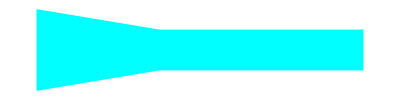

```mathematica
Graphics[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[{

%

}]
}]
```

```mathematica
Clear[ploskev2D,Orientacija];
Orientacija[ploskev2D_]:=Round[
Total[
(If[ArcSin[(-(#[[2]]-#[[1]])[[2]] (#[[3]]-#[[2]])[[1]]+(#[[2]]-#[[1]])[[1]] (#[[3]]-#[[2]])[[2]])/(Norm[#[[2]]-#[[1]]]*Norm[#[[3]]-#[[2]]])]<0,-1,1]*VectorAngle[(#[[2]]-#[[1]]),(#[[3]]-#[[2]])])&/@Table[
{
ploskev2D[[n]],
ploskev2D[[((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev2D]]})[[1]] ]],
ploskev2D[[((If[#==0,n+2,#])&/@{Mod[n+2,Length[ploskev2D]]})[[1]] ]]
},
{n,1,Length[ploskev2D],1}
]
]/(2π)
];

Orientacija[PloskevIz3DV2D[{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}}]]
```

1

Part::partw: Part 6 of {{0.,-1.},{3.,-0.5},{8.,0.5},{3.,0.5},{0.,0.}} does not exist.

Part::partw: Part 7 of {{0.,-1.},{3.,-0.5},{8.,0.5},{3.,0.5},{0.,0.}} does not exist.

Part::partw: Part 6 of {{0.,-1.},{3.,-0.5},{8.,0.5},{3.,0.5},{0.,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

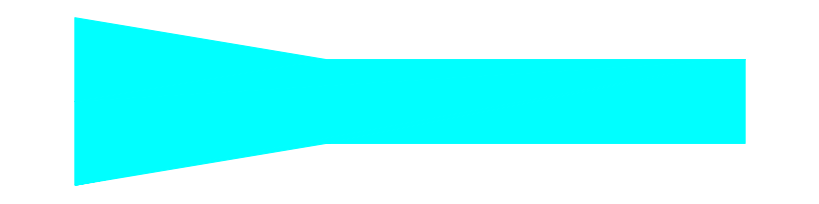

```mathematica
ploskev2D无=PloskevIz3DV2D[{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}}];
ploskev2DOst无=ploskev2D无;
orientacija无=Orientacija[ploskev2D无];
šločeztofazo=0;


trikotniki无=Reap[

While[Length[ploskev2DOst无]>3,(*1 krog*)

Do[
trojica无={
ploskev2DOst无[[n]],
ploskev2DOst无[[((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev2D无]]})[[1]] ]],
ploskev2DOst无[[((If[#==0,n+2,#])&/@{Mod[n+2,Length[ploskev2D无]]})[[1]] ]]
};
If[orientacija无*(-(trojica无[[2]]-trojica无[[1]])[[2]] (trojica无[[3]]-trojica无[[2]])[[1]]+(trojica无[[2]]-trojica无[[1]])[[1]] (trojica无[[3]]-trojica无[[2]])[[2]])>0,
odreži=1;
Do[
odreži*=1-AliSeSekata[
trojica无[[1]],
trojica无[[3]],
ploskev2DOst无[[i]],
ploskev2DOst无[[((If[#==0,i+1,#])&/@{Mod[i+1,Length[ploskev2DOst无]]})[[1]] ]]],
{i,Length[ploskev2DOst无]}];
If[odreži==1,
šločeztofazo++;
Sow[trojica无];
ploskev2DOst无=Delete[ploskev2DOst无,((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev2D无]]})[[1]]]
]
],
{n,1,Length[ploskev2DOst无],1}
]

];
Sow[ploskev2DOst无 ]

][[2]][[1]];
Show[
Graphics[{
RGBColor[0,1,1,1],
EdgeForm[{Thin}],

Polygon[{#}]
}]&/@trikotniki无
]
```

```mathematica
triangulacija无=((Position[ploskev2D无,#][[1,1]])&/@#)&/@trikotniki无
```

{{1,2,3,4,5,6,7}}

```mathematica
((ploskev3D[[#]])&/@#)&/@triangulacija无
```

Part::partd: Part specification ploskev3D⟦1⟧ is longer than depth of object.

Part::partd: Part specification ploskev3D⟦2⟧ is longer than depth of object.

Part::partd: Part specification ploskev3D⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{ploskev3D⟦1⟧,ploskev3D⟦2⟧,ploskev3D⟦3⟧,ploskev3D⟦4⟧,ploskev3D⟦5⟧,ploskev3D⟦6⟧,ploskev3D⟦7⟧}}

```mathematica
Show[
Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[{Thin}],

Polygon[{#}]
}]&/@(((ploskev3D[[#]])&/@#)&/@triangulacija无)
]
```

-Graphics3D-

```mathematica
Clear[ploskev3D];
PloskevNaTrikotnike[ploskev3D_]:={

ploskev2D无=PloskevIz3DV2D[ploskev3D];
ploskev2DOst无=ploskev2D无;
orientacija无=Orientacija[ploskev2D无];
šločeztofazo=0;


trikotniki无=Reap[

While[Length[ploskev2DOst无]>3,(*1 krog*)

Do[
trojica无={
ploskev2DOst无[[n]],
ploskev2DOst无[[((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev2D]]})[[1]] ]],
ploskev2DOst无[[((If[#==0,n+2,#])&/@{Mod[n+2,Length[ploskev2D]]})[[1]] ]]
};
If[orientacija无*(-(trojica无[[2]]-trojica无[[1]])[[2]] (trojica无[[3]]-trojica无[[2]])[[1]]+(trojica无[[2]]-trojica无[[1]])[[1]] (trojica无[[3]]-trojica无[[2]])[[2]])>0,
odreži=1;
Do[
odreži*=1-AliSeSekata[
trojica无[[1]],
trojica无[[3]],
ploskev2DOst无[[i]],
ploskev2DOst无[[((If[#==0,i+1,#])&/@{Mod[i+1,Length[ploskev2DOst无]]})[[1]] ]]],
{i,Length[ploskev2DOst无]}];
If[odreži==1,
šločeztofazo++;
Sow[trojica无];
ploskev2DOst无=Delete[ploskev2DOst无,((If[#==0,n+1,#])&/@{Mod[n+1,Length[ploskev2D]]})[[1]]]
]
],
{n,1,Length[ploskev2DOst无],1}
]

];
Sow[ploskev2DOst无 ]

][[2]][[1]];

((Position[ploskev2D无,#][[1,1]])&/@#)&/@trikotniki无
}[[1]];
PloskevNaTrikotnike[{{0,-1,0},{0,-.5,-3},{0,-.5,-8},{0,.5,-8},{0,.5,-3},{0,1,0},{0,0,0}}]
```

Mod::indet: Indeterminate expression Mod[2,0] encountered.

Part::pkspec1: The expression If[Indeterminate==0,n+1,Indeterminate] cannot be used as a part specification.

Mod::indet: Indeterminate expression Mod[3,0] encountered.

Part::pkspec1: The expression If[Indeterminate==0,n+2,Indeterminate] cannot be used as a part specification.

Part::pkspec1: The expression If[Indeterminate==0,n+1,Indeterminate] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Mod::indet: Indeterminate expression Mod[3,0] encountered.

General::stop: Further output of Mod::indet will be suppressed during this calculation.

$Aborted